# Hitra Fourierova transformacija

## Množenje polinomov

## Različne predstavitve polinomov

Polinom p stopnje n lahko enolično predstavimo na več načinov z N=n+1 vrednostmi:

s seznamom n + 1 koeficientov: p(x) = a_0+a_1 x+⋯ + a_n x^n

časovna zahtevnost seštevanja je O(n)

časovna zahtevnost množenja je O(n^2) - z ustrezno prilagoditvijo tudi O(n^(log 3))

časovna zahtevnost evalvacije v točki je O(n)

z vodilnim koeficientom in seznamom n ničel: p(x) = a_n(x-x_1)(x-x_2)⋯(x-x_n)

časovna zahtevnost seštevanja je neznana, saj moramo razcepiti vsoto razširjenih polinimov

časovna zahtevnost množenja je O(n)

časovna zahtevnost evalvacije v točki je O(n)

z vrednostmi v n + 1 točkah: p(x_0) =y_0,p(x_1) =y_1,…,p(x_n)=y_n

časovna zahtevnost seštevanja je O(n)

časovna zahtevnost množenja je O(n), če sta oba polinoma stopnje <n/2, sicer moramo razširiti vzorce na dodatne točke

časovna zahtevnost evalvacije v točki je O(n)

Iz druge predstavitve enostavno dobimo prvo in tretjo, težava pa je v pretvorbi v drugo smer. Kaj pa tretja predstavitev? V njo enostavno pretvarjamo v času O(n^2), saj  v času O(n) izračunamo vrednost v O(n) točkah.

```mathematica
p[x_]:=3+4x+5 x^2-6 x^3+7 x^5-3 x^7
HornerForm[p[x]]
```

3+x (4+x (5+x (-6+x^2 (7-3 x^2))))

```mathematica
horner[koeficienti_,x_]:=Fold[({a,acc}|->a x+acc),Reverse[koeficienti]]
```

```mathematica
koef:={3,4,5,-6,0,7,0,-3}
horner[koef,2]
```

-177

```mathematica
p[2]
```

-177

```mathematica
vrednosti[koeficienti_,tocke_]:=Map[x|->horner[koeficienti,x],tocke]
```

```mathematica
tocke={-4,-3,-2,-1,0,1,2,3}
```

{-4,-3,-2,-1,0,1,2,3}

```mathematica
vred=vrednosti[koef,tocke]
```

{42435,5058,223,6,3,10,-177,-4962}

Obratno lahko uporabimo Lagrangeovo interpolacijo ∑_(i=0)^n y_i(∏_(j!=i) (x-x_j))/(∏_(j!=i) (x_i-x_j)):

```mathematica
interpoliraj[tocke_,vrednosti_]:=Module[{N=Length[tocke]},
x|->∑_(i=1)^N vrednosti[[i]] ∏_(j=1)^N If[i!=j,(x-tocke[[j]])/(tocke[[i]]-tocke[[j]]),1]
]
```

```mathematica
interpoliraj[tocke,vred][x]//Expand
```

3+4 x+5 x^2-6 x^3+7 x^5-3 x^7

```mathematica
InterpolatingPolynomial[Transpose[{tocke,vred}],x]//Expand
```

3+4 x+5 x^2-6 x^3+7 x^5-3 x^7

## Hitra Fourierova transformacija

Prednost predstavitve z vrednostmi je, da si lahko točke x_0,x_1,…,x_n izberemo poljubno. Na primer, ker velja p(x) = a_0+a_1 x+⋯ + a_n x^n=(a_0+a_2 x^2+⋯)+(a_1+a_3 x^2+⋯)x=p_s(x^2)+x p_l(x^2) lahko vrednost polinoma p v točki x prevedemo na iskanje vrednosti dveh manjših polinomov v točki x^2. Ker je x^2=(-x)^2 na ta način enostavno izračunamo vrednost polinoma v dveh točkah: 
p(1)=p_s(1)+p_l(1)
p(-1)=p_s(1)- p_l(1)
Lahko bi izbrali tudi
p(ⅈ)=p_s(-1)+ⅈ p_l(-1)
p(-ⅈ)=p_s(-1)- ⅈ p_l(-1)
s čimer bi izračun p v 4 točkah prevedli na izračun p_s in p_l v 1 in -1, kar bi nadalje lahko prevedli na:
p_s(1)=p_ss(1)+p_sl(1)
p_s(-1)=p_ss(1)-p_sl(1)
p_l(1)=p_ls(1)+p_ll(1)
p_l(-1)=p_ls(1)+p_ll(1)
Torej izračun p_ss,p_sl,p_ls,p_ll v točki 1.
Če je ω=ⅇ^(2π ⅈ/N) N-ti koren enote, za k<N/2 velja:
p(ω^k)=p_s(ω^(2k))+ω^k p_l(ω^(2k))
p(ω^(N/2+k))=p_s(ω^(2(N/2+k)))+ω^(N/2+k)p_l(ω^(2(N/2+k)))=p_s(ω^(N+2k))+ω^(N/2+k)p_l(ω^(N+2k))=p_s(ω^(2k))+ω^(N/2+k)p_l(ω^(2k))
Faktorjem ω^0,ω^1,…, ki nastopajo pri drugem členu, pravimo faktorji prčkanja (twiddle factors).
To nas privede do rekurzivne definicije:

```mathematica
fft[{x_}]:={x}
fft[koeficienti_]:=Module[{N=Length[koeficienti],sodi,lihi,w,prckanje},
sodi=fft[koeficienti[[1;;N;;2]]];
lihi=fft[koeficienti[[2;;N;;2]]];
w=ⅇ^(2π ⅈ /N);
prckanje=Table[w^k,{k,0,N/2-1}];
Join[sodi+prckanje lihi,sodi-prckanje lihi]
]
```

```mathematica
koreniEnote=Table[ⅇ^((2π ⅈ k)/8),{k,0,7}]
```

{1,ⅇ^((ⅈ π)/4),ⅈ,ⅇ^((3 ⅈ π)/4),-1,ⅇ^(-(3 ⅈ π)/4),-ⅈ,ⅇ^(-(ⅈ π)/4)}

```mathematica
fft[koef]//N
```

{10.,3.+0.757359 ⅈ,-2.+20. ⅈ,3.-9.24264 ⅈ,6.,3.+9.24264 ⅈ,-2.-20. ⅈ,3.-0.757359 ⅈ}

```mathematica
vrednosti[koef,koreniEnote]//N
```

{10.,3.+0.757359 ⅈ,-2.+20. ⅈ,3.-9.24264 ⅈ,6.,3.+9.24264 ⅈ,-2.-20. ⅈ,3.-0.757359 ⅈ}

```mathematica
Fourier[koef,FourierParameters->{1,1}]
```

{10.+0. ⅈ,3.+0.757359 ⅈ,-2.+20. ⅈ,3.-9.24264 ⅈ,6.+0. ⅈ,3.+9.24264 ⅈ,-2.-20. ⅈ,3.-0.757359 ⅈ}

## Inverz hitre Fourierove transformacije

Fourierovo transformacijo lahko zapišemo tudi v matrični obliki:
FFT(a_0
a_1
⋮
a_n)=(p(ω^0)=a_0+a_1 ω+⋯+a_n ω^n
p(ω^2)=a_0+a_1 ω^2+⋯+a_n ω^(2n)
⋮
p(ω^n)=a_0+a_1 ω^n+⋯+a_n ω^(n^2))=(1 | 1 | ⋯ | 1
1 | ω | ⋯ | ω^n
⋮ | ⋮ | ⋱ | ⋮
1 | ω^n | ⋯ | ω^(n^2))(a_0
a_1
⋮
a_n) = W(a_0
a_1
⋮
a_n)
Torej za interpolacijo lahko uporabimo kar inverz matrike W. Če preverimo:
W W̄ = (1 | 1 | ⋯ | 1
1 | ω | ⋯ | ω^n
⋮ | ⋮ | ⋱ | ⋮
1 | ω^n | ⋯ | ω^(n^2))(1 | 1 | ⋯ | 1
1 | ω̄ | ⋯ | OverBar[ω^n]
⋮ | ⋮ | ⋱ | ⋮
1 | OverBar[ω^n] | ⋯ | OverBar[ω^(n^2)])
oziroma
(W W̄)_(i j)=∑_(k=0)^n ω^(i k)(ω̄)^(k j)=∑_(k=0)^n ω^((i-j)k)
Če je i=j, so vsi členi enaki 1, zato je (W W̄)_(i j)=n+1=N, sicer pa imamo geometrijsko vrsto
∑_(k=0)^n ω^((i-j)k)=ω^((i-j)N)=0
zato je W W̄=N I oziroma W^-1=1/N W̄. Inverz lahko torej učinkovito izračunamo na podoben način:

```mathematica
ifft[{x_}]:={x}
ifft[koeficienti_]:=Module[{N=Length[koeficienti],sodi,lihi,w,prckanje},
sodi=ifft[koeficienti[[1;;N;;2]]];
lihi=ifft[koeficienti[[2;;N;;2]]];
w=ⅇ^(2π ⅈ /N);
prckanje=Table[w^-k,{k,0,N/2-1}];
Join[sodi+prckanje lihi,sodi-prckanje lihi]
]/2
```

```mathematica
ifft[fft[koef]]//N
```

{3.,4.-1.11022×10^-16 ⅈ,5.,-6.-1.11022×10^-16 ⅈ,0.,7.+1.11022×10^-16 ⅈ,0.,-3.+1.11022×10^-16 ⅈ}

```mathematica
InverseFourier[fft[koef],FourierParameters->{1,1}]
```

{3.,4.,5.,-6.,0.,7.,0.,-3.}

```mathematica
p={1,1,0,0,0,0,0,0}
```

{1,1,0,0,0,0,0,0}

```mathematica
ifft[fft[p]fft[p]]//FullSimplify
```

{1,2,1,0,0,0,0,0}

## Frekvenčna analiza

## Preprost signal

```mathematica
440. 2^(-9/12)
```

261.626

```mathematica
?TriangleWave
```

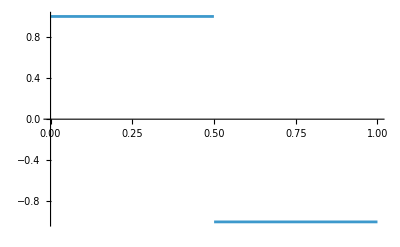

```mathematica
Plot[SquareWave[t],{t,0,1}]
```

```mathematica
c[t_]:=Sin[261*2π t]
```

```mathematica
sample[f_,rate_]:=Most[Table[N[f[t]],{t,0,1,1/rate}]]
```

```mathematica
?SawtoothWave
```

```mathematica
ListPlay[sample[c,1000],SampleRate->1000]
```

-Graphics-

```mathematica
navijNaKrog[f_,rate_]:=
Module[{samples},
samples=sample[f,rate];
Manipulate[
Column[{
coordinates=Table[samples[[i]]{Cos[2π i/rate],Sin[2π i/rate]},{i,rate}];
Graphics[{LightGray,Line[coordinates],Black,Point/@coordinates,Red,Point[f[p]{Cos[2π p],Sin[2π p]}]},Axes->True,PlotRange->{{-1,1},{-1,1}}],
Plot[f[x],{x,0,1},Epilog->{Red,Line[{{p,0},{p,f[p]}}],Point[{p,f[p]}]}]
}
],{p,0,1}
]
]
```

```mathematica
navijNaKrog[t|->Sin[3 2π t],100]
```

```mathematica
navijHitreje[f_,rate_]:=
Module[{samples},
samples=sample[f,rate];
Manipulate[
coordinates=Table[samples[[i]]{Cos[2π k i/rate],Sin[2π k i/rate]},{i,rate}];
average=Plus@@coordinates/rate;
Graphics[{LightGray,Line[coordinates],Black,Point/@coordinates,Red,PointSize[Large],Point[average]},Axes->True,PlotRange->{{-1,1},{-1,1}}],
{{k,1},0,10}
]
]
```

```mathematica
navijHitreje[t|->Abs[Cos[5 π t]],100]
```

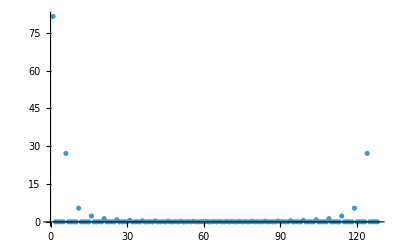

```mathematica
ListPlot[Abs[fft[sample[t|->Abs[Cos[5 π t]],128]]],PlotRange->Full]
```

```mathematica
frekvence[vzorec_]:=ListPlot[
Transpose[{Range[0,Length[vzorec]-1],Abs[Fourier[vzorec]]}],PlotRange->All
]
```

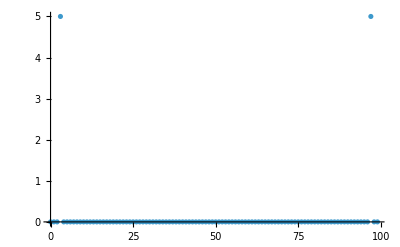

```mathematica
frekvence[sample[t|->Sin[3 2π t],100]]
```

## Sestavljen signal

```mathematica
e[t_]:=Sin[2^(5/12)261 2 Pi t]
```

```mathematica
Play[c[t],{t,0,1}]
```

```mathematica
Play[c[t]-c[t],{t,0,1}]
```

-Graphics-

```mathematica
Play[e[t],{t,0,1}]
```

-Graphics-

```mathematica
terca[t_]:=c[t]+e[t]
```

```mathematica
Play[terca[t],{t,0,1}]
```

-Graphics-

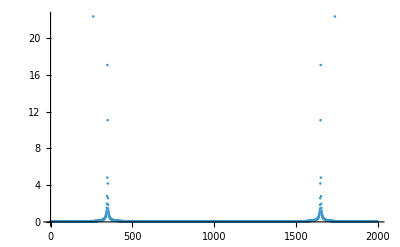

```mathematica
frekvence[sample[terca,2000]]
```

```mathematica
2^(7/12.)
```

1.49831

```mathematica
g[t_]:=Sin[2^(7/12)261 2 Pi t]
```

```mathematica
dur[t_]:=c[t]+e[t]+g[t]
```

```mathematica
Play[dur[t],{t,0,1}]
```

-Graphics-

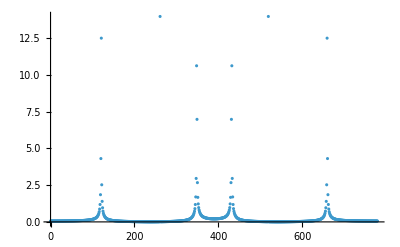

```mathematica
frekvence[sample[dur,3*260]]
```

## Spektrogram

```mathematica
lestvica[t_]:=Piecewise[{{c[t],t<1/3},{e[t],1/3<=t<2/3},{g[t],True}}]
```

```mathematica
ListPlay[sample[lestvica,2000],SampleRate->2000]
```

-Graphics-

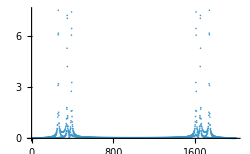

```mathematica
frekvence[sample[lestvica,2000]]
```

```mathematica
spektrogram[vzorec_,c_]:=
ListDensityPlot[Table[Abs[Fourier[podVzorec]],{podVzorec,Partition[vzorec,c]}]]
```

```mathematica
spektrogram[sample[lestvica,2000],20]
```

-Graphics-

```mathematica
Spectrogram[sample[lestvica,2000]]
```

-Graphics-

## Posplošitve FFT

## Končni obsegi

```mathematica
ntt[{x_},_]:={x}
ntt[koeficienti_,p_]:=Module[{N=Length[koeficienti],sodi,lihi,w,prckanje},
sodi=ntt[koeficienti[[1;;N;;2]],p];
lihi=ntt[koeficienti[[2;;N;;2]],p];
w=PowerMod[PrimitiveRoot[p],(p-1)/N,p];
prckanje=Table[PowerMod[w,k,p],{k,0,N/2-1}];
Join[sodi+prckanje lihi,sodi-prckanje lihi]
]
```

```mathematica
intt[{x_},_]:={x}
intt[koeficienti_,p_]:=Mod[PowerMod[2,-1,p]*Module[{N=Length[koeficienti],sodi,lihi,w,prckanje},
sodi=intt[koeficienti[[1;;N;;2]],p];
lihi=intt[koeficienti[[2;;N;;2]],p];
w=PowerMod[PrimitiveRoot[p],(p-1)/N,p];
prckanje=Table[PowerMod[w,-k,p],{k,0,N/2-1}];
Join[sodi+prckanje lihi,sodi-prckanje lihi]
],p]
```

```mathematica
intt[ntt[{1,1,0,0,0,0,0,0},17]*ntt[{1,1,0,0,0,0,0,0},17],17]
```

{1,2,1,0,0,0,0,0}

```mathematica
intt[ntt[{10,10,0,0,0,0,0,0},17]*ntt[{10,10,0,0,0,0,0,0},17],17]
```

{15,13,15,0,0,0,0,0}

```mathematica
Select[Range[1,100]*8+1,PrimeQ]
```

{17,41,73,89,97,113,137,193,233,241,257,281,313,337,353,401,409,433,449,457,521,569,577,593,601,617,641,673,761,769}

```mathematica
intt[ntt[{10,10,0,0,0,0,0,0},41]*ntt[{10,10,0,0,0,0,0,0},41],41]
```

{18,36,18,0,0,0,0,0}

```mathematica
ChineseRemainder[{15,18},{17,41}]
```

100

```mathematica
ChineseRemainder[{13,36},{17,41}]
```

200

## Sestavljena osnova

```mathematica
fft[{x_},{}]:={x}
fft[koeficienti_,{r_,rs___}]:=Module[{N=Length[koeficienti],M,kosi,w,prckanje},
M=N/r;
kosi=Table[fft[koeficienti[[j;;N;;r]],{rs}],{j,1,r}];
w=ⅇ^(2π ⅈ /N);
Flatten[
Table[
Sum[w^((j-1)(q+M t)) kosi[[j,q+1]],{j,1,r}],
{t,0,r-1},{q,0,M-1}
]
]
]
```

```mathematica
ifft[{x_},{}]:={x}
ifft[koeficienti_,{r_,rs___}]:=Module[{N=Length[koeficienti],M,kosi,w,prckanje},
M=N/r;
kosi=Table[fft[koeficienti[[j;;N;;r]],{rs}],{j,1,r}];
w=ⅇ^(2π ⅈ /N);
Flatten[
Table[
Sum[w^((j-1)(q+M t)) kosi[[j,q+1]],{j,1,r}],
{t,0,r-1},{q,0,M-1}]
]/r
]
```

## Praštevilska osnova